```mathematica
Solve[1/(fa-d1)+1/(fc-d+d1)==1/fb,d]
Solve[1/(fa-d1)+1/fc==1/fb,d1]
```

{{d→(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb)}}

{{d1→(fa fb-fa fc+fb fc)/(fb-fc)}}

416.667

69.4444

6.

0.444444

13.5

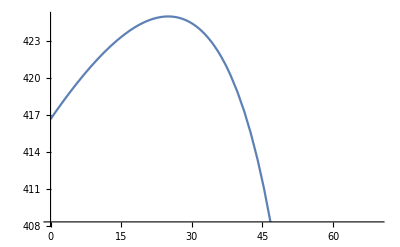

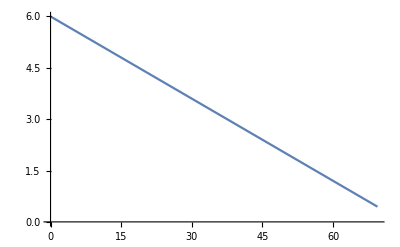

```mathematica
r=1;
fa0=125;
fb0=50;
fc0=500;
d0=(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb)/.{fa->fa0,fb->fb0,fc->fc0,d1->0}//N
dmax=(fa fb-fa fc+fb fc)/(fb-fc)/.{fa->fa0,fb->fb0,fc->fc0}//N
M0=(fc(fa-fb))/(fa fb)/.{fa->fa0,fb->fb0,fc->fc0}//N
Mmin=(fb fc)/(fa(fc-fb))/.{fa->fa0,fb->fb0,fc->fc0}//N
f=((fa-fb)(fc-fb))/fb^2/.{fa->fa0,fb->fb0,fc->fc0}//N
Plot[{(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb),d1}/.{fa->fa0,fb->fb0,fc->fc0},{d1,0,dmax},PlotRange->{0.98d0,1.02d0}]
Plot[((fa-d1) fc)/(fa(fc-(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb)+d1))/.{fa->fa0,fb->fb0,fc->fc0},{d1,0,dmax}]
```

So, by using three lens: +125, -50, +500, and fixing the two convex lens distance to 420mm, and move the concave lens from 0 to 50mm, we can achieve an zoom with magnification from 6 to 2.

511.538

60.4545

6.78261

0.474308

14.3

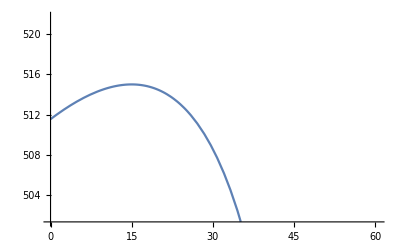

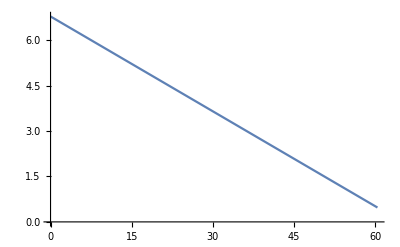

```mathematica
r=1;
fa0=115;
fb0=50;
fc0=600;
d0=(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb)/.{fa->fa0,fb->fb0,fc->fc0,d1->0}//N
dmax=(fa fb-fa fc+fb fc)/(fb-fc)/.{fa->fa0,fb->fb0,fc->fc0}//N
M0=(fc(fa-fb))/(fa fb)/.{fa->fa0,fb->fb0,fc->fc0}//N
Mmin=(fb fc)/(fa(fc-fb))/.{fa->fa0,fb->fb0,fc->fc0}//N
f=((fa-fb)(fc-fb))/fb^2/.{fa->fa0,fb->fb0,fc->fc0}//N
Plot[{(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb),d1}/.{fa->fa0,fb->fb0,fc->fc0},{d1,0,dmax},PlotRange->{0.98d0,1.02d0}]
Plot[((fa-d1) fc)/(fa(fc-(d1^2-d1 fa+fa fb+d1 fc-fa fc+fb fc)/(d1-fa+fb)+d1))/.{fa->fa0,fb->fb0,fc->fc0},{d1,0,dmax}]
```